{0.166619,0.150114,0.121388,0.0923671,0.0678685,0.0488985,0.0349465}

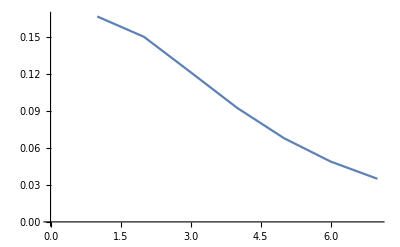

```mathematica
pivotDeviation[N_]:=Abs[Median[RandomReal[{0,1},N]]-0.5]
dataPoints = 1000000;
meanPivotDeviation[N_] := Mean[Table[pivotDeviation[N],{t,1,dataPoints}]]
result =meanPivotDeviation /@{2,4,8,16,32,64, 128}
ListLinePlot[result]
```

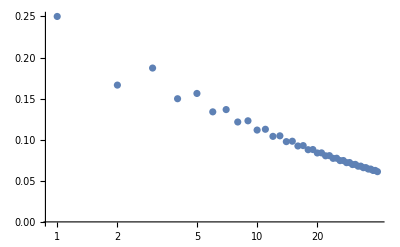

```mathematica
ListLogLinearPlot[result,PlotRange->All]
```

```mathematica
{0.16661869758185202,0.15011397953296568,0.12138823984553046,0.09236706510116163,0.06786848219672782,0.048898516414733806,0.03494649431584174}
```

{0.166619,0.150114,0.121388,0.0923671,0.0678685,0.0488985,0.0349465}

{0.5,0.166667,0.15}

```mathematica
dataPoints = 10000000;
meanPivotDeviation[N_] := Mean[Table[pivotDeviation[N],{t,1,dataPoints}]]
result =meanPivotDeviation /@{64}
```

{0.0488923}

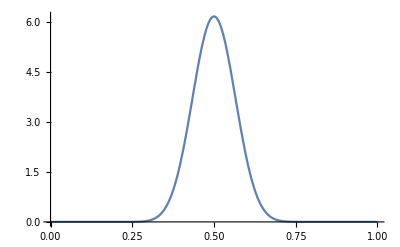

```mathematica
BetaVariance[alpha_,beta_]:=(alpha*beta)/((alpha+beta)*(alpha+beta)*(alpha+beta+1.0))
BetaStdDev[alpha_,beta_]:=Sqrt[BetaVariance[alpha,beta]]
BMB[alpha_,beta_]:=(Gamma[alpha]Gamma[beta]) / Gamma[alpha +beta]
BetaPDF[x_,alpha_,beta_]:=x^(alpha - 1) (1-x)^(beta-1) / BMB[alpha,beta]
Plot[BetaPDF[x,30,30],{x,0,1}]
```